```mathematica
SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mBkg"];
Directory[]
```

C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mBkg

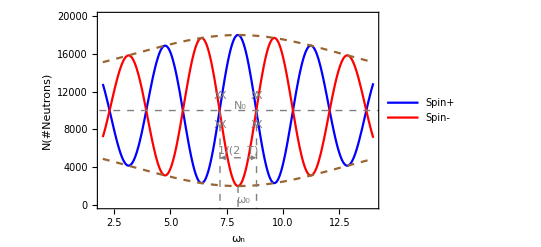

```mathematica
lineStyle={Thin,Gray,Dashed};
line11=Line[{{0,10000},{16,10000}}];
line12=Line[{{8,2000},{8,-2500}}];
lineStyle2={Thin,Gray,Dashed};
lineStyle3={Thick,Gray};
line21=Line[{{8.82,10000},{8.82,-2500}}];
line22=Line[{{7.2,10000},{7.2,-2500}}];
wr=8;wo=8;alpha=.8;
pt1[xx_]:=N[10000(1+alpha*wr^2/((xx-wo)^2+wr^2)Cos[15.44-7(xx*8/29)])];
pt2[xx_]:=N[10000(1-alpha*wr^2/((xx-wo)^2+wr^2)Cos[15.44-7(xx*8/29)])];
pt3[xx_]:=N[10000(1+alpha*wr^2/((xx-wo)^2+wr^2))];
pt4[xx_]:=N[10000(1-alpha*wr^2/((xx-wo)^2+wr^2))];
exp1=Plot[{pt1[xx],pt2[xx],pt3[xx],pt4[xx]},{xx,2,14},Frame->True,Axes->False,PlotRange->{{2,14},{0,20000}},
Epilog->{
{Directive[lineStyle],line11,line12,Text[Style["N_0",FontSize->Large],{29.3*8/29,10500}],Text[Style["ω_0",FontSize->Large],{8.25,550}]},
{Directive[lineStyle2],line21,line22,{Arrowheads[{-.02,.02}],Arrow[{{7.2,5000},{8.82,5000}}]},Text[Style["1/(2  T)",FontSize->Large],{8,5750}]},
{Directive[lineStyle3],Text[Style["X",FontSize->Large],{7.1,11500}],Text[Style["X",FontSize->Large],{7.1,8500}],Text[Style["X",FontSize->Large],{7.3,8500}],Text[Style["X",FontSize->Large],{7.3,11500}],(**)Text[Style["X",FontSize->Large],{8.72,8500}],Text[Style["X",FontSize->Large],{8.72,11500}],Text[Style["X",FontSize->Large],{8.92,11500}],Text[Style["X",FontSize->Large],{8.92,8500}]}
},
FrameLabel->{"ω_n","N(#Neutrons)"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},PlotLegends->{"Spin+","Spin-"},PlotStyle->{Blue,Red,{Brown,Dashed},{Brown,Dashed}},ImageSize->{1000}]
```